## CSS expansion in Mellin Space (Bozzi et. al)

Before running this notebook, create a folder named datfiles in the same directory where this notebook is located.

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Physical constants

```mathematica
nf=5;CA=3;CF=(nf^2-1)/(2nf);
β0=1/12(11 CA-2nf);(*According to Bozzi's definition*)
GF=1.166378 10^-5;
GevtoPb=3.8937966 10^8;
σ0[αs_]:=(αs^2 √2 GF)/(576π);
A1g=CA;B1g=-2β0;
A2g=CA/2(CA(67/18-Zeta[2])-5/9 nf);
B2g=1/(16 π^2)((-64/3-24 Zeta[3])CA^2+16/3 nf CA+4 nf CF)+β0 CA/π Zeta[2];
```

#### Various Definitions

```mathematica
C1gg=0;hh1gg=1/2(11+3 π^2);C1gq[nn_]:=CF/(2(nn+1));
```

```mathematica
Clear[γ,γn,C1,H1];
```

```mathematica
γ[i_,j_]:=Subscript[γ0,StringJoin[ToString/@{i,j}]];
γn[i_,j_]:=Subscript[γ1,StringJoin[ToString/@{i,j}]];
C1[i_,j_]:=Subscript[C1,StringJoin[ToString/@{i,j}]];
```

#### Anomalous Dimensions

```mathematica
(*One Loop Anomalous Dimension*)
γNqq[nn_]:=CF/2(3/2-1/(nn+1)-1/(nn+2)-PolyGamma[nn+1]-2EulerGamma);
γNqg[nn_]:=nf/2(1/(nn+1)-2/(nn+2)+2/(nn+3));
γNgq[nn_]:=CF/2(2/nn-2/(nn+1)+1/(nn+2));
γNgg[nn_]:=CA(1/nn-2/(nn+1)+1/(nn+2)-1/(nn+3)-PolyGamma[nn+1]-EulerGamma+β0);
```

```mathematica
(*Two Loop Anomalous Dimension*)
```

```mathematica
(*Two Loops Anomalous Dimension*)
```

```mathematica
δgg=-2/3 nf+27/4 Zeta[3];
sp1gg[x_]:=1/(1-x)(16.75-(5nf)/6-3/4 π^2);
sp2gg[x_]:=1/(72x(x^2-1))((-1+x) (2 nf (1+x) (-61+x (-9+x (-9+109 x)))+9 x (-(1+x) (25+109 x)+6 π^2 (3+2 x (2+x+x^2))))-12 x (2 nf (-1+x) (1+x)^2+27 (1+x-x^2)^2) Log[x]^2+6 Log[x] (108 (1+x) (1+(-1+x) x)^2 Log[1-x]+(-1+x) (-x (1+x) (225+99 x (-1+4 x)+2 nf (9+13 x))+108 (1+x+x^2)^2 Log[1+x]))+648 (-1+x) (1+x+x^2)^2 PolyLog[2,-x]);
```

```mathematica
γmgg[n_?NumericQ]:=NIntegrate[x^(n-1)sp2gg[x]+(x^(n-1)-1)sp1gg[x],{x,0,1}]+δgg;
```

#### H functions (contain the constant terms when pT→0)

```mathematica
H1[a_,b_]:=KroneckerDelta[g,a]KroneckerDelta[g,b](h1g-(B1+1/2 B1 LQ)LQ-pc β0 LR)+KroneckerDelta[g,a]C1[g,b]+KroneckerDelta[g,b]C1[g,a]+(KroneckerDelta[g,a]γ[g,b]+KroneckerDelta[g,b]γ[g,a])(LF-LQ);
H2[a_,b_]:=0;(*To be implemented*)
```

```mathematica
H1[g,g]/.{KroneckerDelta[c_,d_]:> If[c===d,1,0]}/.{LR->0,LF-> 0,LQ-> 0}
```

h1g+2 C1_gg

#### Σ functions (contain the singular terms when pT→0)

```mathematica
Σ12[a_,b_]:=-A1/2 KroneckerDelta[g,a]KroneckerDelta[g,b];
Σ11[a_,b_]:=-(KroneckerDelta[g,a]KroneckerDelta[g,b](B1+A1 LQ)+KroneckerDelta[g,a]γ[g,b]+KroneckerDelta[g,b]γ[g,a]);
Σ24[a_,b_]:=(A1)^2/8 KroneckerDelta[g,a]KroneckerDelta[g,b];
Σ23[a_,b_]:=-A1(1/3 β0 KroneckerDelta[g,a]KroneckerDelta[g,b]+1/2 Σ11[a,b]);
ξ[m_,n_,a_,b_]:=Σ11[m,n](KroneckerDelta[m,a]γ[n,b]+KroneckerDelta[n,b]γ[m,a]);
Σ22[a_,b_]:=-A1/2(H1[a,b]-β0 KroneckerDelta[g,a]KroneckerDelta[g,b](LR-LQ))-1/2(A2 KroneckerDelta[g,a] KroneckerDelta[g,b]+(B1+A1 LQ-β0)Σ11[a,b])-1/2(ξ[g,g,a,b]+ξ[g,q,a,b]+ξ[q,g,a,b]+ξ[q,q,a,b]);
χ[m_,n_,a_,b_]:=H1[m,n](KroneckerDelta[m,a]KroneckerDelta[n,b](B1+A1 LQ)+KroneckerDelta[m,a]γ[n,b]+KroneckerDelta[n,b]γ[m,a]);
Σ21[a_,b_]:=Σ11[a,b]β0(LQ-LR)-(χ[g,g,a,b]+χ[g,q,a,b]+χ[q,g,a,b]+χ[q,q,a,b])-(KroneckerDelta[g,a]KroneckerDelta[g,b](B2+A2 LQ)-β0(KroneckerDelta[g,a]C1[g,b]+KroneckerDelta[g,b]C1[g,a]+KroneckerDelta[g,a]γn[g,b]+KroneckerDelta[g,b]γn[g,a]));
```

#### Fourier Inverse of Log(χ) where χ=1+b^2 Q^2/b0^2:

```mathematica
IC1[pt_,mH_]:=-b0/x BesselK[1,b0 x]/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC2[pt_,mH_]:=(2 b0)/x(BesselK[1, b0 x]Log[x]-Derivative[1,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC3[pt_,mH_]:=-(3 b0)/x(BesselK[1, b0 x](Log[x]^2-Zeta[2])-2 Derivative[1,0][BesselK][1,b0 x]Log[x]+Derivative[2,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
IC4[pt_,mH_]:=(4b0)/x(BesselK[1, b0 x](Log[x]^3-3 Zeta[2]Log[x]+2Zeta[3])-3 Derivative[1,0][BesselK][1,b0 x](Log[x]^2-Zeta[2])+3 Derivative[2,0][BesselK][1,b0 x]Log[x]-Derivative[3,0][BesselK][1,b0 x])/.{x-> pt/mH,b0-> 2 Exp[-EulerGamma]};
```

#### Fourier Inverse of Log(χ) where χ=b^2 Q^2/b0^2:

```mathematica
FC1[pt_,mH_]:=-1/x^2/.{x-> pt/mH};
FC2[pt_,mH_]:=-2/x^2 Log[1/x^2]/.{x-> pt/mH};
FC3[pt_,mH_]:=-3/x^2 Log[1/x^2]^2/.{x-> pt/mH};
FC4[pt_,mH_]:=-4/x^2(Log[1/x^2]^3-4Zeta[3])/.{x-> pt/mH};
```

Up to αs-terms

```mathematica
αss=0.11264;nn=3;pt=10;Q=125;mH=125;μR=125;μF=125;NN=1.5;
```

```mathematica
dσLO[αs_,a_,b_]:=σ0[αs](αsp(Σ12[a,b] LC2+Σ11[a,b] LC1(*+H1[a,b]*)))/.{KroneckerDelta[c_,d_]:> If[c===d,1,0]}/.{αsp-> (αs/π)} (*αsp=αs/π*)
```

```mathematica
dσLOgg[αs_,nn_,pt_,Q_,mH_,μR_,μF_]:=(2 pt)/mH^2 (GevtoPb)dσLO[αs,g,g]/.{LC1-> FC1[pt,mH],LC2-> FC2[pt,mH]}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[nn+1]}/.h1g-> hh1gg/.{Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg}/.{A1-> A1g,B1-> B1g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2]};
```

```mathematica
cssNNLLexpLOaspt=Table[{pt,dσLOgg[αss,nn+1,pt,Q,mH,μR,μF]},{pt,1,150}];(*To compare to threshold N-> N-> N+1*)
Export["./datfiles/cssNNLLexpLOaspt.dat",cssNNLLexpLOaspt,"Table"];
```

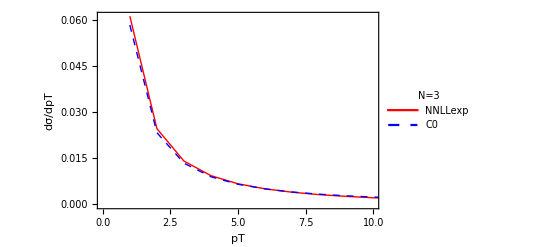

```mathematica
(*Requires threshold-corrected-expansion.nb*)
ListLinePlot[{Import["./datfiles/cssNNLLexpLOaspt.dat","Table"],Import["./datfiles/C0expLOaspt.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},PlotLegends->Placed[LineLegend[{"NNLLexp","C0"},LabelStyle->{Black,10},LegendLabel->"N=3",LegendFunction->"Frame"],{0.7,0.35}],FrameLabel->{{"dσ/dpT",""},{"pT", "NNLL pT expanded to LO"}},PlotRange->{{0,10},All}]
(*also normalized by GevtoPb*)
```

```mathematica
NNLLexpLOLargeNSmallpt=Table[{pt,1/(σ0[αss] GevtoPb)dσLOgg[αss,NN,pt,Q,mH,μR,μF]},{pt,1,30}](*small-pt & large-N*);
Export["./datfiles/NNLLexpLOLargeNSmallpt.dat",NNLLexpLOLargeNSmallpt,"Table"];
```

Up to αs^2-terms

```mathematica
αss=0.108316;nn=4;pt=5;Q=125;mH=125;μR=125;μF=125;
```

```mathematica
dσNLO[αs_,a_,b_]:=dσLO[αs,a,b]+σ0[αs] αsp^2((Σ24[a,b] LC4+Σ23[a,b] LC3+Σ22[a,b] LC2+Σ21[a,b]LC1+H2[a,b]))/.{KroneckerDelta[c_,d_]:> If[c===d,1,0]} /.{αsp-> (αs/π)}(*αsp=αs/π*)
```

```mathematica
dσNLOgg[αs_,nn_,pt_,Q_,mH_,μR_,μF_]:=(2 pt)/mH^2 (GevtoPb)dσNLO[αs,g,g]/.{LC1-> FC1[pt,mH],LC2-> FC2[pt,mH],LC3-> FC3[pt,mH],LC4-> FC4[pt,mH]}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[nn],Subscript[γ0,StringJoin[ToString/@{g,q}]]-> γNgq[nn],
Subscript[γ0,StringJoin[ToString/@{q,g}]]-> γNqg[nn],Subscript[γ0,StringJoin[ToString/@{q,q}]]-> γNqq[nn],
Subscript[γ1,StringJoin[ToString/@{g,g}]]-> γmgg[nn]}/.{Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg,
Subscript[C1,StringJoin[ToString/@{g,q}]]-> C1gq[nn]}/.{A1-> A1g,A2-> A2g,B1-> B1g,B2-> B2g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2]}/.h1g-> hh1gg;
```

```mathematica
cssNNLLexpNLOaspt=Table[{pt,1/(σ0[αss] GevtoPb)dσNLOgg[αss,nn+1,pt,Q,mH,μR,μF]},{pt,1,40}];(*To compare to threshold N-> N-> N+1*)
Export["./datfiles/cssNNLLexpNLOaspt.dat",cssNNLLexpNLOaspt,"Table"];
```

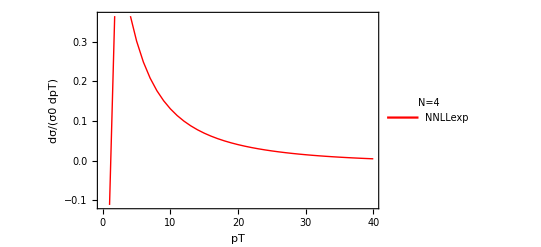

```mathematica
ListLinePlot[Import["./datfiles/cssNNLLexpNLOaspt.dat","Table"],Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{Thick,Red},PlotLegends->Placed[LineLegend[{"NNLLexp"},LabelStyle->{Black,10},LegendLabel->"N=4",LegendFunction->"Frame"],{0.7,0.7}],FrameLabel->{{"dσ/(σ0 dpT)",""},{"pT", "NNLL pT expanded to NLO"}}]
(*also normalized by GevtoPb*)
```

```mathematica
NNLLexpNLOLargeNSmallpt=Table[{pt,1/(σ0[αss] GevtoPb)dσNLOgg[αss,NN,pt,Q,mH,μR,μF]},{pt,1,30}](*small-pt & large-N*);
Export["./datfiles/NNLLexpNLOLargeNSmallpt.dat",NNLLexpNLOLargeNSmallpt,"Table"];
```

Analytical limits (useful for the combination)

For the combination, the following logs of pT will replace the logs of pT that appear in the Threshold resummed expression.

```mathematica
Clear[nf,CA,CF,β0,GF,σ0];
```

#### Large-N limits of the Anomalous Dimensions:

```mathematica
γgqLargeN=0;
γqgLargeN=0;
γggLargeN=-CA(LN+EulerGamma);(*LN=Log[n]*)
```

#### Analytical expansions:

```mathematica
(*Up to αs-terms in the expansion*)
```

```mathematica
dσLOagg=Select[1/σ0[αs] dσLO[αs,g,g]/.{LC1-> FC1[pT,MH],LC2-> FC2[pT,MH]}/.{Log[MH^2/pT^2]-> -LpT,LQ-> 0}//Expand,MemberQ[#,pT^_(*LpT|LpT^_*)]&];
(*Keep only terms that are logarithmically enhanced when pT->0*)
resLOagg=Collect[dσLOagg/.{A1/π-> A1th},{αs,LpT}]
```

αs (-(A1th LpT MH^2)/pT^2+(B1 MH^2)/(π pT^2)+(2 MH^2 γ0_gg)/(π pT^2))

```mathematica
dσLOaggLargeN=Select[1/σ0[αs] dσLO[αs,g,g]/.{LC1-> FC1[pT,MH],LC2-> FC2[pT,MH]}/.{Log[MH^2/pT^2]-> -LpT,LQ-> 0}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γggLargeN}//Expand,MemberQ[#,pT^_(*LpT|LpT^_*)]&];
(*Keep only terms that are logarithmically enhanced when pT->0 & γ-> γ(N-> ∞)*)
resLOaggLargeN=Collect[dσLOaggLargeN/.{A1/π-> Ath},{αs,LpT}]
```

(-(Ath LpT MH^2)/pT^2+(B1 MH^2)/(π pT^2)-(2 CA EulerGamma MH^2)/(π pT^2)-(2 CA LN MH^2)/(π pT^2)) αs

```mathematica
(*Up to αs^2-terms in the expansion*)
```

```mathematica
(*small-pt NOT large-N*)
dσNLOagg=Select[1/σ0[αp] dσNLO[αp,g,g]/.{LC1-> FC1[pT,MH],LC2-> FC2[pT,MH],LC3-> FC3[pT,MH],LC4-> FC4[pT,MH]}/.{Log[MH^2/pT^2]-> -LpT}/.{LR-> 0,LF-> 0,LQ-> 0}//Expand,MemberQ[#,pT^_(*LpT|LpT^_*)]&];
resNLOagg=Collect[Normal@Series[dσNLOagg,{αsp,0,2}],{αsp,LpT}]
```

(B1 MH^2 αp)/(π pT^2)+(B2 MH^2 αp^2)/(π^2 pT^2)+(B1 h1g MH^2 αp^2)/(π^2 pT^2)+(A1^2 LpT^3 MH^2 αp^2)/(2 π^2 pT^2)+(2 B1 MH^2 αp^2 C1_gg)/(π^2 pT^2)-(2 MH^2 αp^2 β0 C1_gg)/(π^2 pT^2)+(2 MH^2 αp γ0_gg)/(π pT^2)+(2 h1g MH^2 αp^2 γ0_gg)/(π^2 pT^2)+(4 MH^2 αp^2 C1_gg γ0_gg)/(π^2 pT^2)+LpT^2 (-(3 A1 B1 MH^2 αp^2)/(2 π^2 pT^2)+(A1 MH^2 αp^2 β0)/(π^2 pT^2)-(3 A1 MH^2 αp^2 γ0_gg)/(π^2 pT^2))+(2 MH^2 αp^2 C1_gq γ0_qg)/(π^2 pT^2)+LpT (-(A1 MH^2 αp)/(π pT^2)-(A2 MH^2 αp^2)/(π^2 pT^2)+(B1^2 MH^2 αp^2)/(π^2 pT^2)-(A1 h1g MH^2 αp^2)/(π^2 pT^2)-(B1 MH^2 αp^2 β0)/(π^2 pT^2)-(2 A1 MH^2 αp^2 C1_gg)/(π^2 pT^2)+(4 B1 MH^2 αp^2 γ0_gg)/(π^2 pT^2)-(2 MH^2 αp^2 β0 γ0_gg)/(π^2 pT^2)+(4 MH^2 αp^2 γ0_gg^2)/(π^2 pT^2)+(2 MH^2 αp^2 γ0_gq γ0_qg)/(π^2 pT^2))-(2 MH^2 αp^2 β0 γ1_gg)/(π^2 pT^2)+(2 A1^2 MH^2 αp^2 Zeta[3])/(π^2 pT^2)

```mathematica
dσNLOaggLargeN=Select[1/σ0[αp] dσNLO[αp,g,g]/.{LC1-> FC1[pT,MH],LC2-> FC2[pT,MH],LC3-> FC3[pT,MH],LC4-> FC4[pT,MH]}/.{Log[MH^2/pT^2]-> -LpT}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γggLargeN,
Subscript[γ0,StringJoin[ToString/@{g,q}]]-> γgqLargeN,Subscript[γ0,StringJoin[ToString/@{q,g}]]-> γqgLargeN,Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg}/.{LR-> 0,LF-> 0,LQ-> 0}//Expand,
MemberQ[#,pT^_(*LpT|LpT^_*)]&];(*Keep only terms that are enhanced when pT->0 & γ-> γ(N-> ∞)*)
resNLOaggLargeN=Collect[Normal@Series[dσNLOaggLargeN,{αsp,0,2}],{αsp,LpT}]
```

(B1 MH^2 αp)/(π pT^2)-(2 CA EulerGamma MH^2 αp)/(π pT^2)-(2 CA LN MH^2 αp)/(π pT^2)+(B2 MH^2 αp^2)/(π^2 pT^2)+(B1 h1g MH^2 αp^2)/(π^2 pT^2)-(2 CA EulerGamma h1g MH^2 αp^2)/(π^2 pT^2)-(2 CA h1g LN MH^2 αp^2)/(π^2 pT^2)+(A1^2 LpT^3 MH^2 αp^2)/(2 π^2 pT^2)+LpT^2 (-(3 A1 B1 MH^2 αp^2)/(2 π^2 pT^2)+(3 A1 CA EulerGamma MH^2 αp^2)/(π^2 pT^2)+(3 A1 CA LN MH^2 αp^2)/(π^2 pT^2)+(A1 MH^2 αp^2 β0)/(π^2 pT^2))+LpT (-(A1 MH^2 αp)/(π pT^2)-(A2 MH^2 αp^2)/(π^2 pT^2)+(B1^2 MH^2 αp^2)/(π^2 pT^2)-(4 B1 CA EulerGamma MH^2 αp^2)/(π^2 pT^2)+(4 CA^2 EulerGamma^2 MH^2 αp^2)/(π^2 pT^2)-(A1 h1g MH^2 αp^2)/(π^2 pT^2)-(4 B1 CA LN MH^2 αp^2)/(π^2 pT^2)+(8 CA^2 EulerGamma LN MH^2 αp^2)/(π^2 pT^2)+(4 CA^2 LN^2 MH^2 αp^2)/(π^2 pT^2)-(B1 MH^2 αp^2 β0)/(π^2 pT^2)+(2 CA EulerGamma MH^2 αp^2 β0)/(π^2 pT^2)+(2 CA LN MH^2 αp^2 β0)/(π^2 pT^2))-(2 MH^2 αp^2 β0 γ1_gg)/(π^2 pT^2)+(2 A1^2 MH^2 αp^2 Zeta[3])/(π^2 pT^2)

#### Make sure that the large-N expansion is correct:

```mathematica
nf=5;CA=3;β0=1/12(11 CA-2nf);mH=125;CF=(nf^2-1)/(2nf);
```

```mathematica
dσLOaFuncgg[αss_,n_,pt_]:=(2 pt)/mH^2 dσLOagg/.{pT-> pt,LpT-> -Log[MH^2/pt^2]}/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[n]}/.{αs-> αss,MH-> mH}/.{A1-> A1g,B1-> B1g};
LimitNNLLexpLOSmallpt=Table[{pt,dσLOaFuncgg[αss,NN,pt]},{pt,1,30}](*small-pt & large-N*);
Export["./datfiles/LimitNNLLexpLOSmallpt.dat",LimitNNLLexpLOSmallpt,"Table"];
```

```mathematica
dσLOaFuncggLargeN[αss_,n_,pt_]:=(2 pt)/mH^2 dσLOaggLargeN/.{pT-> pt,LpT-> -Log[MH^2/pt^2],LN-> Log[n]}/.{αs-> αss,MH-> mH}/.{A1-> A1g,B1-> B1g};
LimitNNLLexpLOSmallptLargeN=Table[{pt,dσLOaFuncggLargeN[αss,NN,pt]},{pt,1,30}];(*small-pt & large-N*)
Export["./datfiles/LimitNNLLexpLOSmallptLargeN.dat",LimitNNLLexpLOSmallptLargeN,"Table"];
```

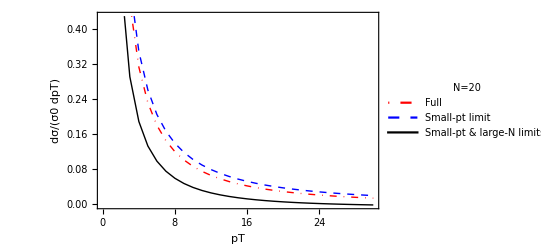

```mathematica
ListLinePlot[{Import["./datfiles/NNLLexpLOLargeNSmallpt.dat","Table"],Import["./datfiles/LimitNNLLexpLOSmallpt.dat","Table"],Import["./datfiles/LimitNNLLexpLOSmallptLargeN.dat","Table"]},
PlotStyle->{{Thick,DotDashed,Red},{Thick,Dashed,Blue},{Thick,Black}},Frame->True,FrameStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Full","Small-pt limit","Small-pt & large-N limits"},
LabelStyle->{Black,10},LegendLabel->"N=20",LegendFunction->"Frame"],{0.6,0.7}],FrameLabel->{{"dσ/(σ0 dpT)",""},{"pT", "NNLL pT expanded to LO"}}]
(*also normalized by GevtoPb*)
```

```mathematica
(*NLO expansion in the small-pt limit*)
dσNLOaFuncgg[αs_,n_,pt_]:=(2 pt)/mH^2 dσNLOagg/.LpT-> -Log[MH^2/pt^2]/.{Subscript[γ0,StringJoin[ToString/@{g,g}]]-> γNgg[n],Subscript[γ0,StringJoin[ToString/@{g,q}]]-> γNgq[n],
Subscript[γ0,StringJoin[ToString/@{q,g}]]-> γNqg[n],Subscript[γ0,StringJoin[ToString/@{q,q}]]-> γNqq[n],Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg,
Subscript[γ1,StringJoin[ToString/@{g,g}]]-> γmgg[n],Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg,Subscript[C1,StringJoin[ToString/@{g,q}]]-> C1gq[n],
 A1-> A1g,A2-> A2g,B1-> B1g,B2-> B2g}/.h1g-> hh1gg/.{pT-> pt,αp-> αs,MH-> mH};
LimitNNLLexpNLOSmallpt=Table[{pt,dσNLOaFuncgg[αss,NN,pt]},{pt,1,30}](*small-pt & large-N*);
Export["./datfiles/LimitNNLLexpNLOSmallpt.dat",LimitNNLLexpNLOSmallpt,"Table"];
```

```mathematica
(*NLO expansion in the small-pt & Large-N limit*)
dσNLOaFuncggLargeN[αs_,n_,pt_]:=(2 pt)/mH^2 dσNLOaggLargeN/.{LpT-> -Log[MH^2/pt^2],LN-> Log[n]}/.{Subscript[γ1,StringJoin[ToString/@{g,g}]]-> γmgg[n],
Subscript[C1,StringJoin[ToString/@{g,g}]]-> C1gg,Subscript[C1,StringJoin[ToString/@{g,q}]]-> C1gq[n], A1-> A1g,A2-> A2g,B1-> B1g,
B2-> B2g,h1g-> hh1gg,pT-> pt,αp-> αs,MH-> mH};
LimitNNLLexpNLOSmallptLargeN=Table[{pt,dσNLOaFuncggLargeN[αss,NN,pt]},{pt,1,30}](*small-pt & large-N*);
Export["./datfiles/LimitNNLLexpNLOSmallptLargeN.dat",LimitNNLLexpNLOSmallptLargeN,"Table"];
```

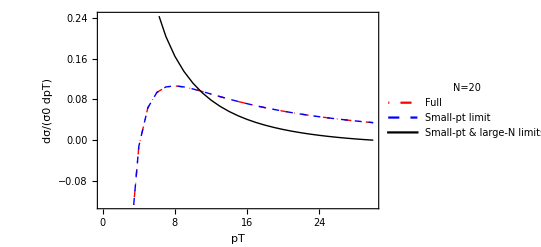

```mathematica
ListLinePlot[{Import["./datfiles/NNLLexpNLOLargeNSmallpt.dat","Table"],Import["./datfiles/LimitNNLLexpNLOSmallpt.dat","Table"],Import["./datfiles/LimitNNLLexpNLOSmallptLargeN.dat","Table"]},
PlotStyle->{{Thick,DotDashed,Red},{Thick,Dashed,Blue},{Thick,Black}},Frame->True,FrameStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Full","Small-pt limit","Small-pt & large-N limits"},
LabelStyle->{Black,10},LegendLabel->"N=20",LegendFunction->"Frame"],{0.7,0.8}],FrameLabel->{{"dσ/(σ0 dpT)",""},{"pT", "NNLL pT expanded to NLO"}}]
(*also normalized by GevtoPb*)
```

Appendix

#### Analytical expression of the coefficients:

```mathematica
Σ12[g,g](*Coefficient of LC2 in gg-channel*)
```

-A1/2

```mathematica
Σ11[g,g]/.{B1-> -2β0}(*Coefficient of LC1 in gg-channel*)
```

-A1 LQ+2 β0-2 γ0_gg

#### re-Check that χ=b^2 Q^2/b0^2 and χ=1+b^2 Q^2/b0^2 are equivalent in x-space when pt→0:

```mathematica
Map[{IC1[#,125],FC1[#,125]}&,{1,5,10}]//N
```

{{-15621.6,-15625.},{-622.655,-625.},{-154.34,-156.25}}

```mathematica
Map[{IC2[#,125],FC2[#,125]}&,{1,5,10}]//N (*Investigate this Difference*)
```

{{-301741.,-301770.},{-8034.75,-8047.19},{-1571.16,-1578.58}}

```mathematica
Map[{IC3[#,125],FC3[#,125]}&,{1,5,10}]//N
```

{{-4.37083×10^6,-4.37112×10^6},{-77624.2,-77708.7},{-11920.1,-11961.2}}

```mathematica
Map[{IC4[#,125],FC4[#,125]}&,{1,5,10}]//N
```

{{-5.59771×10^7,-5.59798×10^7},{-654510.,-655005.},{-77389.3,-77556.8}}